```mathematica
coef[k_]:=-2/(Pi(1+4 k^2))(ⅇ^(-π/2)*(-1)^k-1)(1-2 I k)
```

```mathematica
func[x_]=∑_(k=-30)^30 coef[k]*ⅇ^(I 2 k x);
```

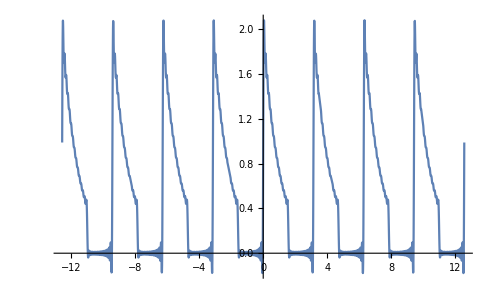

```mathematica
Plot[func[x],{x,-4 Pi,4 Pi}]
```